# Data preprocessing: Saiz et al 2020 data set NANOG, GATA6 (NANOG rb, GATA6 gt antibodies)

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
shiftValue[expName_,val_,threshold_,experiments_]:=Switch[expName,experiments[[1,1]],val+(threshold[[1]]-threshold[[1]]),experiments[[2,1]],val+(threshold[[1]]-threshold[[2]]),experiments[[3,1]],val+(threshold[[1]]-threshold[[3]]),experiments[[4,1]],val+(threshold[[1]]-threshold[[4]])]
```

```mathematica
zCorrection[fileName_,slope_,channels_:{"Dapi","Nanog","Gata6","Gata4"}]:=Block[{nucleiFeatures,nucleiFeaturesWithCorr,exportFName},
nucleiFeatures="NucleiFeatures"/.Import[fileName];
nucleiFeaturesWithCorr=Join[#,
Table[channels[[i]]<>"-AvgLnCorr"->Log[channels[[i]]<>"-Avg"/.#]-slope[[i]]*("Centroid"/.#)[[3]],{i,1,Length[channels]}]&@#]&/@nucleiFeatures;
exportFName=StringReplace[fileName,"Features.mx"->"Features_ZCorrected.mx"];
Export[exportFName,"NucleiFeatures"->nucleiFeaturesWithCorr]
]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colourNegPos[i_]:={Lighter[Gray,0.3],Darker[Gray,0.7]}[[i]]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7],Darker[Cyan,0.5]}[[i]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Look at data

```mathematica
fNames=FileNames["*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
ablatLMSRaw=Import[fNames[[1]]];
```

```mathematica
ablatLMS=MapThread[Rule,{ablatLMSRaw[[1]],#}]&/@ablatLMSRaw[[2;;-1]];
```

```mathematica
ablatLMS[[1]]//Keys
```

{Experiment,Treatment,Genotype1,Litter,Embryo_ID,Cell_ID,TE_ICM,Cell_cycle,Size,X,Y,Z,CH1.Avg,CH1.Sum,CH2.Avg,CH2.Sum,CH3.Avg,CH3.Sum,CH4.Avg,CH4.Sum,CH5.Avg,CH5.Sum,Exp_date,Img_date,Gene1,Gene2,Genotype2,Gene3,Genotype3,Background,target,target_t0,target_killed,Cellcount_t0,Recovery,Cell_diff,Experimenter,MINS_correct,Cellcount,icm.count,group.median,Stage.t0,litter.median.t0,Channel,Marker,ab.2,CH2.marker,CH1.ebLogCor,CH2.ebLogCor,CH3.ebLogCor,CH5.ebLogCor,CH3.ebLogCor.x,CH1.ebLogCor.s,CH2.ebLogCor.s,CH3.ebLogCor.s,CH5.ebLogCor.s,CH3.ebLogCor.xs,CH3.ebLogCor.xl,CH5.ebLogCor.xl,Identity.km,id.cluster,Identity.hc}

```mathematica
experiments=DeleteDuplicates["Experiment"/.ablatLMS]
```

{062317Abl_AO.Littermate.Pdgfra.wt,062317Abl_AP.Littermate.Pdgfra.wt,062817Abl_AQ.Littermate.Pdgfra.wt,062817Abl_AR.Littermate.Pdgfra.wt,062817Abl_AS.Littermate.Pdgfra.wt,071217Abl_AV.Littermate.Pdgfra.wt,072517Abl_AW.Littermate.Pdgfra.wt,072517Abl_AX.Littermate.Pdgfra.wt,072817Abl_AY.Littermate.Pdgfra.wt,072817Abl_AZ.Littermate.Pdgfra.wt,080117Abl_BA.Littermate.Pdgfra.wt,080117Abl_BB.Littermate.Pdgfra.wt,080117Abl_BC.Littermate.Pdgfra.wt,080117Abl_BD.Littermate.Pdgfra.wt,081417Abl_BH.Littermate.Pdgfra.wt,081517Abl_BK.Littermate.Pdgfra.wt,102218Abl_DV.Littermate.Pdgfra.wt,102218Abl_DW.Littermate.Pdgfra.wt,111318Abl_DZ.Littermate.Pdgfra.wt,082219Abl_FG.Littermate.Pdgfra.het,082219Abl_FG.Littermate.Pdgfra.wt,082819Abl_FI.Littermate.Pdgfra.wt,082819Abl_FJ.Littermate.Pdgfra.wt,040317Abl_Q.Littermate.Pdgfra.wt,040317Abl_R.Littermate.Pdgfra.wt,040317Abl_S.Littermate.Pdgfra.wt,040317Abl_T.Littermate.Pdgfra.wt,040517Abl_U.Littermate.Pdgfra.wt,040517Abl_V.Littermate.Pdgfra.wt,041117Abl_W.Littermate.Pdgfra.wt,012318Abl_CJ.Littermate.Pdgfra.wt,013018Abl_CK.Littermate.Pdgfra.wt,013118Abl_CLb.Littermate.Pdgfra.wt,013118Abl_CLa.Littermate.Pdgfra.wt,013118Abl_CMb.Littermate.Pdgfra.wt,013118Abl_CMa.Littermate.Pdgfra.wt,013118Abl_CNa.Littermate.Pdgfra.wt,013118Abl_CNb.Littermate.Pdgfra.wt,020618Abl_CQ.Littermate.Pdgfra.wt,072318Abl_DP.Littermate.Pdgfra.wt,072318Abl_DQ.Littermate.Pdgfra.wt,072518Abl_DR.Littermate.Pdgfra.wt,072518Abl_DS.Littermate.Pdgfra.wt,102218Abl_DX.Littermate.Pdgfra.wt,110817Abl_BY.Littermate.Pdgfra.wt,112018Abl_EA.Littermate.Pdgfra.wt,121018Abl_EB.Littermate.Pdgfra.wt,121018Abl_EC.Littermate.Pdgfra.wt,121917Abl_CD.Littermate.Pdgfra.wt,121917Abl_CE.Littermate.Pdgfra.wt}

ablat_if.csv contains infos on imaging channels

```mathematica
ablatIFRaw=Import[FileNameJoin[{NotebookDirectory[],"References","ablat_if.csv"}]];
```

```mathematica
ablatIF=MapThread[Rule,{ablatIFRaw[[1]],#}]&/@ablatIFRaw[[2;;-1]];
```

```mathematica
ablatIF[[1]]//Keys
```

{Experiment,Litter,Genotype1,Treatment,Channel,Marker,ab.2}

```mathematica
DeleteDuplicates[Select[{"Experiment","Genotype1","Channel","Marker"}/.ablatIF,StringContainsQ[#[[4]],"GATA6."]||StringContainsQ[#[[4]],"NANOG."]&]]
```

{{082515_Pd-abl,wt,CH4,GATA6.gt},{082515_Pd-abl,wt,CH5,NANOG.rb},{082515_Pd-abl,het,CH4,GATA6.gt},{082515_Pd-abl,het,CH5,NANOG.rb},{082615_Pd-abl,wt,CH4,GATA6.gt},{082615_Pd-abl,wt,CH5,NANOG.rb},{082615_Pd-abl,het,CH4,GATA6.gt},{082615_Pd-abl,het,CH5,NANOG.rb},{103115_Pd-abl,wt,CH4,GATA6.gt},{103115_Pd-abl,wt,CH5,NANOG.rb},{103115_Pd-abl,het,CH4,GATA6.gt},{103115_Pd-abl,het,CH5,NANOG.rb},{110215_Pd-abl,wt,CH4,GATA6.gt},{110215_Pd-abl,wt,CH5,NANOG.rb},{110215_Pd-abl,het,CH4,GATA6.gt},{110215_Pd-abl,het,CH5,NANOG.rb},{110315_Pd-abl,wt,CH4,GATA6.gt},{110315_Pd-abl,wt,CH5,NANOG.rb},{110315_Pd-abl,het,CH4,GATA6.gt},{110315_Pd-abl,het,CH5,NANOG.rb},{032217Abl_F,het,CH3,NANOG.rb},{032217Abl_F,het,CH5,GATA6.gt},{032217Abl_F,wt,CH3,NANOG.rb},{032217Abl_F,wt,CH5,GATA6.gt},{032217Abl_G,het,CH3,NANOG.rb},{032217Abl_G,het,CH5,GATA6.gt},{032217Abl_G,wt,CH3,NANOG.rb},{032217Abl_G,wt,CH5,GATA6.gt},{032717Abl_K,het,CH3,NANOG.rb},{032717Abl_K,het,CH5,GATA6.gt},{032717Abl_K,wt,CH3,NANOG.rb},{032717Abl_K,wt,CH5,GATA6.gt},{032717Abl_L,het,CH3,NANOG.rb},{032717Abl_L,het,CH5,GATA6.gt},{032717Abl_L,wt,CH3,NANOG.rb},{032717Abl_L,wt,CH5,GATA6.gt},{032717Abl_N,het,CH3,NANOG.rb},{032717Abl_N,het,CH5,GATA6.gt},{032717Abl_N,wt,CH3,NANOG.rb},{032717Abl_N,wt,CH5,GATA6.gt},{040317Abl_Q,het,CH3,NANOG.rb},{040317Abl_Q,het,CH5,GATA6.gt},{040317Abl_Q,wt,CH3,NANOG.rb},{040317Abl_Q,wt,CH5,GATA6.gt},{040317Abl_R,het,CH3,NANOG.rb},{040317Abl_R,het,CH5,GATA6.gt},{040317Abl_R,wt,CH3,NANOG.rb},{040317Abl_R,wt,CH5,GATA6.gt},{040317Abl_S,het,CH3,NANOG.rb},{040317Abl_S,het,CH5,GATA6.gt},{040317Abl_S,wt,CH3,NANOG.rb},{040317Abl_S,wt,CH5,GATA6.gt},{040317Abl_T,het,CH3,NANOG.rb},{040317Abl_T,het,CH5,GATA6.gt},{040317Abl_T,wt,CH3,NANOG.rb},{040317Abl_T,wt,CH5,GATA6.gt},{040517Abl_U,het,CH3,NANOG.rb},{040517Abl_U,het,CH5,GATA6.gt},{040517Abl_U,wt,CH3,NANOG.rb},{040517Abl_U,wt,CH5,GATA6.gt},{040517Abl_V,het,CH3,NANOG.rb},{040517Abl_V,het,CH5,GATA6.gt},{040517Abl_V,wt,CH3,NANOG.rb},{040517Abl_V,wt,CH5,GATA6.gt},{041117Abl_W,het,CH3,NANOG.rb},{041117Abl_W,het,CH5,GATA6.gt},{041117Abl_W,wt,CH3,NANOG.rb},{041117Abl_W,wt,CH5,GATA6.gt},{041117Abl_X,het,CH3,NANOG.rb},{041117Abl_X,het,CH5,GATA6.gt},{041117Abl_X,wt,CH3,NANOG.rb},{041117Abl_X,wt,CH5,GATA6.gt},{041117Abl_Y,het,CH3,NANOG.rb},{041117Abl_Y,het,CH5,GATA6.gt},{041117Abl_Y,wt,CH3,NANOG.rb},{041117Abl_Y,wt,CH5,GATA6.gt},{041117Abl_Z,het,CH3,NANOG.rb},{041117Abl_Z,het,CH5,GATA6.gt},{041117Abl_Z,wt,CH3,NANOG.rb},{041117Abl_Z,wt,CH5,GATA6.gt},{062317Abl_AO,het,CH3,NANOG.rb},{062317Abl_AO,het,CH5,GATA6.gt},{062317Abl_AO,wt,CH3,NANOG.rb},{062317Abl_AO,wt,CH5,GATA6.gt},{062317Abl_AP,het,CH3,NANOG.rb},{062317Abl_AP,het,CH5,GATA6.gt},{062317Abl_AP,wt,CH3,NANOG.rb},{062317Abl_AP,wt,CH5,GATA6.gt},{062817Abl_AQ,het,CH3,NANOG.rb},{062817Abl_AQ,het,CH5,GATA6.gt},{062817Abl_AQ,wt,CH3,NANOG.rb},{062817Abl_AQ,wt,CH5,GATA6.gt},{062817Abl_AR,het,CH3,NANOG.rb},{062817Abl_AR,het,CH5,GATA6.gt},{062817Abl_AR,wt,CH3,NANOG.rb},{062817Abl_AR,wt,CH5,GATA6.gt},{062817Abl_AS,het,CH3,NANOG.rb},{062817Abl_AS,het,CH5,GATA6.gt},{062817Abl_AS,wt,CH3,NANOG.rb},{062817Abl_AS,wt,CH5,GATA6.gt},{071217Abl_AV,het,CH3,NANOG.rb},{071217Abl_AV,het,CH5,GATA6.gt},{071217Abl_AV,wt,CH3,NANOG.rb},{071217Abl_AV,wt,CH5,GATA6.gt},{072517Abl_AW,het,CH3,NANOG.rb},{072517Abl_AW,het,CH5,GATA6.gt},{072517Abl_AW,wt,CH3,NANOG.rb},{072517Abl_AW,wt,CH5,GATA6.gt},{072517Abl_AX,het,CH3,NANOG.rb},{072517Abl_AX,het,CH5,GATA6.gt},{072517Abl_AX,wt,CH3,NANOG.rb},{072517Abl_AX,wt,CH5,GATA6.gt},{072817Abl_AY,het,CH3,NANOG.rb},{072817Abl_AY,het,CH5,GATA6.gt},{072817Abl_AY,wt,CH3,NANOG.rb},{072817Abl_AY,wt,CH5,GATA6.gt},{072817Abl_AZ,het,CH3,NANOG.rb},{072817Abl_AZ,het,CH5,GATA6.gt},{072817Abl_AZ,wt,CH3,NANOG.rb},{072817Abl_AZ,wt,CH5,GATA6.gt},{080117Abl_BA,het,CH3,NANOG.rb},{080117Abl_BA,het,CH5,GATA6.gt},{080117Abl_BA,wt,CH3,NANOG.rb},{080117Abl_BA,wt,CH5,GATA6.gt},{080117Abl_BB,het,CH3,NANOG.rb},{080117Abl_BB,het,CH5,GATA6.gt},{080117Abl_BB,wt,CH3,NANOG.rb},{080117Abl_BB,wt,CH5,GATA6.gt},{080117Abl_BC,het,CH3,NANOG.rb},{080117Abl_BC,het,CH5,GATA6.gt},{080117Abl_BC,wt,CH3,NANOG.rb},{080117Abl_BC,wt,CH5,GATA6.gt},{080117Abl_BD,het,CH3,NANOG.rb},{080117Abl_BD,het,CH5,GATA6.gt},{080117Abl_BD,wt,CH3,NANOG.rb},{080117Abl_BD,wt,CH5,GATA6.gt},{080217Abl_BF,het,CH3,NANOG.rb},{080217Abl_BF,het,CH5,GATA6.gt},{080217Abl_BF,wt,CH3,NANOG.rb},{080217Abl_BF,wt,CH5,GATA6.gt},{080217Abl_BG,het,CH3,NANOG.rb},{080217Abl_BG,het,CH5,GATA6.gt},{080217Abl_BG,wt,CH3,NANOG.rb},{080217Abl_BG,wt,CH5,GATA6.gt},{081417Abl_BH,het,CH3,NANOG.rb},{081417Abl_BH,het,CH5,GATA6.gt},{081417Abl_BH,wt,CH3,NANOG.rb},{081417Abl_BH,wt,CH5,GATA6.gt},{081517Abl_BJ,wt,CH2,NANOG.rat},{081517Abl_BK,het,CH3,NANOG.rb},{081517Abl_BK,het,CH5,GATA6.gt},{081517Abl_BK,wt,CH3,NANOG.rb},{081517Abl_BK,wt,CH5,GATA6.gt},{081517Abl_BL,wt,CH2,NANOG.rat},{092717Abl_BU,wt,CH2,NANOG.rat},{110817Abl_BY,het,CH3,NANOG.rb},{110817Abl_BY,het,CH5,GATA6.gt},{110817Abl_BY,wt,CH2,NANOG.rat},{110817Abl_BY,wt,CH5,GATA6.gt},{121917Abl_CD,het,CH3,NANOG.rb},{121917Abl_CD,het,CH5,GATA6.gt},{121917Abl_CD,wt,CH2,NANOG.rat},{121917Abl_CD,wt,CH5,GATA6.gt},{121917Abl_CE,het,CH3,NANOG.rb},{121917Abl_CE,het,CH5,GATA6.gt},{121917Abl_CE,wt,CH2,NANOG.rat},{121917Abl_CE,wt,CH5,GATA6.gt},{122617Abl_CF,het,CH3,NANOG.rb},{122617Abl_CF,het,CH5,GATA6.gt},{122617Abl_CF,wt,CH2,NANOG.rat},{122617Abl_CF,wt,CH5,GATA6.gt},{122617Abl_CG,het,CH3,NANOG.rb},{122617Abl_CG,het,CH5,GATA6.gt},{122617Abl_CG,wt,CH2,NANOG.rat},{122617Abl_CG,wt,CH5,GATA6.gt},{122617Abl_CH,het,CH3,NANOG.rb},{122617Abl_CH,het,CH5,GATA6.gt},{122617Abl_CH,wt,CH2,NANOG.rat},{122617Abl_CH,wt,CH5,GATA6.gt},{012318Abl_CJ,het,CH3,NANOG.rb},{012318Abl_CJ,het,CH5,GATA6.gt},{012318Abl_CJ,wt,CH2,NANOG.rat},{012318Abl_CJ,wt,CH5,GATA6.gt},{013018Abl_CK,het,CH3,NANOG.rb},{013018Abl_CK,het,CH5,GATA6.gt},{013018Abl_CK,wt,CH2,NANOG.rat},{013018Abl_CK,wt,CH5,GATA6.gt},{013118Abl_CLa,het,CH3,NANOG.rb},{013118Abl_CLa,het,CH5,GATA6.gt},{013118Abl_CLa,wt,CH2,NANOG.rat},{013118Abl_CLa,wt,CH5,GATA6.gt},{013118Abl_CLb,wt,CH2,NANOG.rat},{013118Abl_CLb,wt,CH3,GATA6.rb},{013118Abl_CMa,het,CH3,NANOG.rb},{013118Abl_CMa,het,CH5,GATA6.gt},{013118Abl_CMa,wt,CH2,NANOG.rat},{013118Abl_CMa,wt,CH5,GATA6.gt},{013118Abl_CMb,wt,CH2,NANOG.rat},{013118Abl_CMb,wt,CH3,GATA6.rb},{013118Abl_CNa,het,CH3,NANOG.rb},{013118Abl_CNa,het,CH5,GATA6.gt},{013118Abl_CNa,wt,CH2,NANOG.rat},{013118Abl_CNa,wt,CH5,GATA6.gt},{013118Abl_CNb,wt,CH2,NANOG.rat},{013118Abl_CNb,wt,CH3,GATA6.rb},{020618Abl_CO,wt,CH2,NANOG.rat},{020618Abl_CO,wt,CH3,GATA6.rb},{020618Abl_CP,wt,CH2,NANOG.rat},{020618Abl_CP,wt,CH3,GATA6.rb},{020618Abl_CQ,het,CH3,NANOG.rb},{020618Abl_CQ,wt,CH2,NANOG.rat},{020618Abl_CQ,wt,CH3,GATA6.rb},{022018Abl_CS,wt,CH2,NANOG.rat},{050818Abl_DA,het,CH3,NANOG.rb},{050818Abl_DA,het,CH5,GATA6.gt},{050818Abl_DA,wt,CH3,NANOG.rb},{050818Abl_DA,wt,CH5,GATA6.gt},{050818Abl_DB,het,CH3,NANOG.rb},{050818Abl_DB,het,CH5,GATA6.gt},{050818Abl_DB,wt,CH3,NANOG.rb},{050818Abl_DB,wt,CH5,GATA6.gt},{052218Abl_DC,het,CH3,NANOG.rb},{052218Abl_DC,het,CH5,GATA6.gt},{052218Abl_DC,wt,CH3,NANOG.rb},{052218Abl_DC,wt,CH5,GATA6.gt},{052318Abl_DD,het,CH3,NANOG.rb},{052318Abl_DD,het,CH5,GATA6.gt},{052318Abl_DD,wt,CH3,NANOG.rb},{052318Abl_DD,wt,CH5,GATA6.gt},{071718Abl_DM,wt,CH2,NANOG.rat},{071718Abl_DM,wt,CH5,GATA6.gt},{071718Abl_DN,wt,CH2,NANOG.rat},{071718Abl_DN,wt,CH5,GATA6.gt},{072318Abl_DP,het,CH3,NANOG.rb},{072318Abl_DP,het,CH5,GATA6.gt},{072318Abl_DP,wt,CH2,NANOG.rat},{072318Abl_DP,wt,CH5,GATA6.gt},{072318Abl_DQ,het,CH3,NANOG.rb},{072318Abl_DQ,het,CH5,GATA6.gt},{072318Abl_DQ,wt,CH2,NANOG.rat},{072318Abl_DQ,wt,CH5,GATA6.gt},{072518Abl_DR,het,CH3,NANOG.rb},{072518Abl_DR,het,CH5,GATA6.gt},{072518Abl_DR,wt,CH2,NANOG.rat},{072518Abl_DR,wt,CH5,GATA6.gt},{072518Abl_DS,het,CH3,NANOG.rb},{072518Abl_DS,het,CH5,GATA6.gt},{072518Abl_DS,wt,CH2,NANOG.rat},{072518Abl_DS,wt,CH5,GATA6.gt},{102218Abl_DV,het,CH3,NANOG.rb},{102218Abl_DV,het,CH5,GATA6.gt},{102218Abl_DV,wt,CH3,NANOG.rb},{102218Abl_DV,wt,CH5,GATA6.gt},{102218Abl_DW,het,CH3,NANOG.rb},{102218Abl_DW,het,CH5,GATA6.gt},{102218Abl_DW,wt,CH3,NANOG.rb},{102218Abl_DW,wt,CH5,GATA6.gt},{102218Abl_DX,het,CH3,NANOG.rb},{102218Abl_DX,het,CH5,GATA6.gt},{102218Abl_DX,wt,CH2,NANOG.rat},{102218Abl_DX,wt,CH5,GATA6.gt},{111318Abl_DZ,het,CH3,NANOG.rb},{111318Abl_DZ,het,CH5,GATA6.gt},{111318Abl_DZ,wt,CH3,NANOG.rb},{111318Abl_DZ,wt,CH5,GATA6.gt},{112018Abl_EA,het,CH3,NANOG.rb},{112018Abl_EA,het,CH5,GATA6.gt},{112018Abl_EA,wt,CH2,NANOG.rat},{112018Abl_EA,wt,CH5,GATA6.gt},{121018Abl_EB,het,CH3,NANOG.rb},{121018Abl_EB,het,CH5,GATA6.gt},{121018Abl_EB,wt,CH2,NANOG.rat},{121018Abl_EB,wt,CH5,GATA6.gt},{121018Abl_EC,het,CH3,NANOG.rb},{121018Abl_EC,het,CH5,GATA6.gt},{121018Abl_EC,wt,CH2,NANOG.rat},{121018Abl_EC,wt,CH5,GATA6.gt},{121718Abl_ED,het,CH3,NANOG.rb},{121718Abl_ED,het,CH5,GATA6.gt},{121718Abl_ED,wt,CH2,NANOG.rat},{121718Abl_ED,wt,CH5,GATA6.gt},{121818Abl_EE,het,CH3,NANOG.rb},{121818Abl_EE,het,CH5,GATA6.gt},{121818Abl_EE,wt,CH2,NANOG.rat},{121818Abl_EE,wt,CH5,GATA6.gt},{121918Abl_EF,het,CH3,NANOG.rb},{121918Abl_EF,het,CH5,GATA6.gt},{121918Abl_EF,wt,CH2,NANOG.rat},{121918Abl_EF,wt,CH5,GATA6.gt},{010319Abl_EG,het,CH3,NANOG.rb},{010319Abl_EG,het,CH5,GATA6.gt},{010319Abl_EG,wt,CH2,NANOG.rat},{010319Abl_EG,wt,CH5,GATA6.gt},{010719Abl_EH,het,CH3,NANOG.rb},{010719Abl_EH,het,CH5,GATA6.gt},{012119Abl_EI,het,CH3,NANOG.rb},{012119Abl_EI,het,CH5,GATA6.gt},{012119Abl_EI,wt,CH2,NANOG.rat},{012119Abl_EI,wt,CH5,GATA6.gt},{012219Abl_EJ,het,CH3,NANOG.rb},{012219Abl_EJ,het,CH5,GATA6.gt},{012219Abl_EJ,wt,CH2,NANOG.rat},{012219Abl_EJ,wt,CH5,GATA6.gt},{021119Abl_EK,het,CH3,NANOG.rb},{021119Abl_EK,het,CH5,GATA6.gt},{021119Abl_EK,wt,CH2,NANOG.rat},{021119Abl_EK,wt,CH5,GATA6.gt},{021119Abl_EL,het,CH3,NANOG.rb},{021119Abl_EL,het,CH5,GATA6.gt},{021119Abl_EL,wt,CH2,NANOG.rat},{021119Abl_EL,wt,CH5,GATA6.gt},{021119Abl_EM,het,CH3,NANOG.rb},{021119Abl_EM,het,CH5,GATA6.gt},{021119Abl_EM,wt,CH2,NANOG.rat},{021119Abl_EM,wt,CH5,GATA6.gt},{021919Abl_EN,het,CH3,NANOG.rb},{021919Abl_EN,het,CH5,GATA6.gt},{021919Abl_EN,wt,CH2,NANOG.rat},{021919Abl_EN,wt,CH5,GATA6.gt},{021919Abl_EO,het,CH3,NANOG.rb},{021919Abl_EO,het,CH5,GATA6.gt},{021919Abl_EO,wt,CH2,NANOG.rat},{021919Abl_EO,wt,CH5,GATA6.gt},{031819Abl_ES,het,CH3,NANOG.rb},{031819Abl_ES,het,CH5,GATA6.gt},{031819Abl_ES,wt,CH2,NANOG.rat},{031819Abl_ES,wt,CH5,GATA6.gt},{031919Abl_ET,het,CH3,NANOG.rb},{031919Abl_ET,het,CH5,GATA6.gt},{031919Abl_ET,wt,CH2,NANOG.rat},{031919Abl_ET,wt,CH5,GATA6.gt},{032019Abl_EU,het,CH3,NANOG.rb},{032019Abl_EU,het,CH5,GATA6.gt},{032019Abl_EU,wt,CH2,NANOG.rat},{032019Abl_EU,wt,CH5,GATA6.gt},{032819Abl_EV,het,CH3,NANOG.rb},{032819Abl_EV,het,CH5,GATA6.gt},{032819Abl_EV,wt,CH2,NANOG.rat},{032819Abl_EV,wt,CH5,GATA6.gt},{050619Abl_EW,het,CH3,NANOG.rb},{050619Abl_EW,het,CH5,GATA6.gt},{050619Abl_EW,wt,CH2,NANOG.rat},{050619Abl_EW,wt,CH5,GATA6.gt},{050819Abl_EX,het,CH3,NANOG.rb},{050819Abl_EX,het,CH5,GATA6.gt},{050819Abl_EX,wt,CH2,NANOG.rat},{050819Abl_EX,wt,CH5,GATA6.gt},{050819Abl_EY,het,CH3,NANOG.rb},{050819Abl_EY,het,CH5,GATA6.gt},{050819Abl_EY,wt,CH2,NANOG.rat},{050819Abl_EY,wt,CH5,GATA6.gt},{050819Abl_EZ,het,CH3,NANOG.rb},{050819Abl_EZ,het,CH5,GATA6.gt},{050819Abl_EZ,wt,CH2,NANOG.rat},{050819Abl_EZ,wt,CH5,GATA6.gt},{051419Abl_FA,het,CH3,NANOG.rb},{051419Abl_FA,het,CH5,GATA6.gt},{051419Abl_FA,wt,CH2,NANOG.rat},{051419Abl_FA,wt,CH5,GATA6.gt},{052119Abl_FB,het,CH3,NANOG.rb},{052119Abl_FB,het,CH5,GATA6.gt},{052119Abl_FB,wt,CH2,NANOG.rat},{052119Abl_FB,wt,CH5,GATA6.gt},{052119Abl_FC,het,CH3,NANOG.rb},{052119Abl_FC,het,CH5,GATA6.gt},{052119Abl_FC,wt,CH2,NANOG.rat},{052119Abl_FC,wt,CH5,GATA6.gt},{052819Abl_FD,het,CH3,NANOG.rb},{052819Abl_FD,het,CH5,GATA6.gt},{052819Abl_FD,wt,CH2,NANOG.rat},{052819Abl_FD,wt,CH5,GATA6.gt},{070919Abl_FE,het,CH3,NANOG.rb},{070919Abl_FE,het,CH5,GATA6.gt},{070919Abl_FE,wt,CH2,NANOG.rat},{070919Abl_FE,wt,CH5,GATA6.gt},{070919Abl_FF,het,CH3,NANOG.rb},{070919Abl_FF,het,CH5,GATA6.gt},{070919Abl_FF,wt,CH2,NANOG.rat},{070919Abl_FF,wt,CH5,GATA6.gt},{082619Abl_FH,het,CH3,NANOG.rb},{082619Abl_FH,het,CH5,GATA6.gt},{082619Abl_FH,wt,CH2,NANOG.rat},{082619Abl_FH,wt,CH5,GATA6.gt},{082219Abl_FG,wt,CH3,NANOG.rb},{082219Abl_FG,wt,CH5,GATA6.gt},{082219Abl_FG,het,CH3,NANOG.rb},{082219Abl_FG,het,CH5,GATA6.gt},{082819Abl_FI,wt,CH3,NANOG.rb},{082819Abl_FI,wt,CH5,GATA6.gt},{082819Abl_FJ,wt,CH3,NANOG.rb},{082819Abl_FJ,wt,CH5,GATA6.gt},{092319Abl_FK,het,CH3,NANOG.rb},{092319Abl_FK,het,CH5,GATA6.gt},{092319Abl_FK,wt,CH2,NANOG.rat},{092319Abl_FK,wt,CH5,GATA6.gt},{100719Abl_FL,wt,CH2,NANOG.rat},{100719Abl_FL,wt,CH5,GATA6.gt},{100719Abl_FL,het,CH3,NANOG.rb},{100719Abl_FL,het,CH5,GATA6.gt},{100719Abl_FM,wt,CH2,NANOG.rat},{100719Abl_FM,wt,CH5,GATA6.gt},{100719Abl_FM,het,CH3,NANOG.rb},{100719Abl_FM,het,CH5,GATA6.gt},{100819Abl_FN,wt,CH2,NANOG.rat},{100819Abl_FN,wt,CH5,GATA6.gt},{100819Abl_FN,het,CH3,NANOG.rb},{100819Abl_FN,het,CH5,GATA6.gt}}

## Convert data into our format

scaling from these images: 
1Aug17_Ablation_BA6_Littermate.lsm, 23Mar17_I12_Littermate.lsm, 26May17Pdgfra_AF6.lsm, 28Jun17_Ablation_AS7_Littermate.lsm (sample from images on figshare):  
0.2767553,0.2767553,1

imaging channels given in *_if.csv

find all littermates in DataFromMINS
split by Embryo_ID and generate one file per embryo
get channel information from *_if.csv file
convert embryo file

### function

```mathematica
Options[convertFromSaiz2020]={"XinMicrons"->0.277,"YinMicrons"->0.277,"ZinMicrons"->1.0}
```

{XinMicrons→0.277,YinMicrons→0.277,ZinMicrons→1.}

```mathematica
convertFromSaiz2020[embryoData_,ifData_,dataType_,opts:OptionsPattern[]]:=Block[{experiment,embryoInfos,ifInfos,channelNaming,nucleiMeasuresRelevant,nucleiMeasuresCorrected,outputFileName,xum=OptionValue["XinMicrons"],yum=OptionValue["YinMicrons"],zum=OptionValue["ZinMicrons"]},
experiment="Experiment"/.embryoData[[1]];
ifInfos=Which[dataType=="ablat",
	embryoInfos={"Experiment"->#[[1]], "Genotype1"->#[[-1]],"Treatment"->#[[2]]}&@(StringSplit[experiment,"."]);
Select[ifData,("Experiment"/.#)==("Experiment"/.embryoInfos)&&("Genotype"/.#)==("Genotype"/.embryoInfos)&&("Treatment"/.#)==("Treatment"/.embryoInfos)&],
dataType=="compounds",
Select[ifData,("Experiment"/.#)==experiment&],
dataType=="escXim",
embryoInfos={"Experiment"->#[[1]],"Treatment"->#[[2]]}&@(StringSplit[experiment,"."]);
Select[ifData,("Experiment"/.#)==("Experiment"/.embryoInfos)&&("Treatment"/.#)==("Treatment"/.embryoInfos)&],
dataType=="new",
embryoInfos={"Experiment"->#[[1]],"Genotype1"->#[[2]]}&@(StringSplit[experiment,"."]);
Select[ifData,("Experiment"/.#)==("Experiment"/.embryoInfos)&&("Genotype1"/.#)==("Genotype1"/.embryoInfos)&],
True,
Print["no rules for this data type available"]
];
channelNaming=MapThread[Rule,{(#<>"."&/@("Channel"/.ifInfos)),(#<>"-"&/@("Marker"/.ifInfos))}];
nucleiMeasuresRelevant=MapThread[Rule,{StringReplace[Keys[#],channelNaming],Values[#]}]&/@embryoData;
nucleiMeasuresCorrected={"NucleiFeatures"->((DeleteCases[#,Rule["",""]]&/@nucleiMeasuresRelevant)/.Rule["Size",s_]->Rule["Size",s*xum*yum*zum]/.{a__,PatternSequence["X"->x_,"Y"->y_,"Z"->z_],b__}->{a,"Centroid"->{xum*x,yum*y,zum*z},b})};
outputFileName=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures",("Embryo_ID"/.nucleiMeasuresRelevant[[1]])<>"_Features.mx"}];
Export[outputFileName,nucleiMeasuresCorrected]
]
```

### Conversion

```mathematica
fNames=FileNames["*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]]
```

#### ablat-lms

```mathematica
ablatLMSRaw=Import[fNames[[1]]];
```

```mathematica
ablatLMS=MapThread[Rule,{ablatLMSRaw[[1]],#}]&/@ablatLMSRaw[[2;;-1]];
```

```mathematica
ablatLMSPerEmbryo=SplitBy[SortBy[Select[ablatLMS,("Treatment"/.#)=="Littermate"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
ablatLMSPerEmbryo//Length
```

176

```mathematica
Length/@ablatLMSPerEmbryo
```

{63,73,75,84,67,75,63,64,62,64,64,62,62,64,71,63,94,75,80,62,68,65,107,114,110,99,88,109,94,105,71,48,63,44,65,64,64,62,57,45,77,78,74,65,71,82,78,31,31,32,32,31,69,64,63,64,71,69,59,60,45,64,92,58,60,34,38,75,80,92,66,65,86,61,65,98,89,87,111,97,76,88,68,64,86,80,68,71,91,94,91,88,99,94,107,74,85,86,79,69,78,68,63,71,71,62,64,106,78,37,92,54,54,64,62,52,70,99,61,64,62,31,32,63,30,50,19,14,32,38,41,33,38,32,30,34,26,35,31,43,44,52,61,49,59,42,32,48,63,60,47,77,77,91,92,64,49,60,86,93,119,98,81,67,68,80,67,86,68,65,115,118,103,106,104,101}

```mathematica
ablatIFRaw=Import[FileNameJoin[{NotebookDirectory[],"References","ablat_if.csv"}]];
```

```mathematica
ablatIF=MapThread[Rule,{ablatIFRaw[[1]],#}]&/@ablatIFRaw[[2;;-1]];
```

```mathematica
ablatIF[[1]]
```

{Experiment→082515_Pd-abl,Litter→082515_Pd,Genotype1→wt,Treatment→,Channel→CH1,Marker→DNA,ab.2→Hoechst}

```mathematica
ablatLMSPerEmbryo[[1,1]]
```

{Experiment→012318Abl_CJ.Littermate.Pdgfra.wt,Treatment→Littermate,Genotype1→wt,Litter→CJ,Embryo_ID→012318Abl_CJ6,Cell_ID→1,TE_ICM→TE,Cell_cycle→I,Size→7633,X→227.69,Y→225.71,Z→7.938,CH1.Avg→2448.1,CH1.Sum→18700000,CH2.Avg→468.29,CH2.Sum→3570000,CH3.Avg→152.67,CH3.Sum→1170000,CH4.Avg→644.8,CH4.Sum→4920000,CH5.Avg→850.06,CH5.Sum→6490000,Exp_date→20180123,Img_date→20180130,Gene1→Pdgfra,Gene2→R26,Genotype2→wt,Gene3→Fgf4,Genotype3→wt,Background→CD1/mixed,target→none,target_t0→NA,target_killed→0,Cellcount_t0→63,Recovery→0min,Cell_diff→zero,Experimenter→NS,MINS_correct→tbd,Cellcount→63,icm.count→25,group.median→73,Stage.t0→[70,90),litter.median.t0→73,Channel→CH2,Marker→NANOG.rat,ab.2→af488.rat,CH2.marker→NANOG.rat,CH1.ebLogCor→8.06984,CH2.ebLogCor→6.40235,CH3.ebLogCor→5.20886,CH5.ebLogCor→7.00278,CH3.ebLogCor.x→5.98321,CH1.ebLogCor.s→0.849327,CH2.ebLogCor.s→0.753866,CH3.ebLogCor.s→0.645629,CH5.ebLogCor.s→0.82246,CH3.ebLogCor.xs→0.737397,CH3.ebLogCor.xl→0.737397,CH5.ebLogCor.xl→0.846678,Identity.km→TE,id.cluster→0,Identity.hc→TE}

```mathematica
convertFromSaiz2020[#,ablatIF,"ablat"]&/@ablatLMSPerEmbryo
```

#### ablat-t0: no littermates

#### compounds

```mathematica
compoundsRaw=Import[fNames[[3]]];
```

```mathematica
compounds=MapThread[Rule,{compoundsRaw[[1]],#}]&/@compoundsRaw[[2;;-1]];
```

```mathematica
compoundsPerEmbryo=SplitBy[SortBy[Select[compounds,("Treatment"/.#)=="Littermate"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
compoundsPerEmbryo//Length
```

136

```mathematica
Length/@compoundsPerEmbryo
```

{138,104,104,125,195,174,188,220,197,216,147,196,130,180,61,145,81,103,105,104,91,90,90,99,98,99,93,93,107,104,91,102,113,125,132,141,159,116,163,166,172,147,152,92,140,148,164,176,196,217,185,183,175,207,173,182,91,84,91,93,85,92,105,103,104,106,152,151,172,105,117,123,124,121,113,118,118,158,132,186,169,174,135,215,177,201,202,230,211,167,160,182,94,105,104,104,88,84,94,79,88,84,90,67,69,63,66,32,65,72,69,58,65,62,130,147,133,118,152,159,155,177,169,166,178,154,107,154,144,153,143,133,134,129,146,171}

```mathematica
compoundsPerEmbryo[[1,1]]
```

{Experiment→011618G6G4_P,Litter→P,Embryo_ID→011618G6G4_P1,Cell_ID→3,TE_ICM→TE,Cell_cycle→I,Size→8735,X→231.44,Y→227.54,Z→5.7944,CH1.Avg→2431.7,CH1.Sum→21200000,CH2.Avg→69.278,CH2.Sum→605000,CH3.Avg→109.99,CH3.Sum→961000,CH4.Avg→596.94,CH4.Sum→5210000,CH5.Avg→352.33,CH5.Sum→3080000,Exp_date→20180116,Img_date→20180124,Gene1→Gata6,Genotype1→het,Gene2→Gata4,Genotype2→ko,Background→CD1/mixed,Treatment→Littermate,Experimenter→NS,MINS_correct→NS,Cellcount→138,icm.count→50,litter.median→125,Stage→120_150,Channel→CH2,Marker→NANOG.rat,ab.2→af488.rat,CH2.marker→NANOG.rat,CH1.ebLogCor→8.08141,CH2.ebLogCor→4.35897,CH3.ebLogCor→4.84303,CH5.ebLogCor→6.03377,CH3.ebLogCor.x→3.90032,CH1.ebLogCor.s→0.822084,CH2.ebLogCor.s→0.568946,CH3.ebLogCor.s→0.626909,CH5.ebLogCor.s→0.702911,CH3.ebLogCor.xs→0.53674,nanog.ab→ratty,Identity.km→TE,CH3.ebLogCor.xl→0.53674,CH5.ebLogCor.xl→0.702911,id.cluster→0,Identity.hc→TE}

```mathematica
compoundsIFRaw=Import[FileNameJoin[{NotebookDirectory[],"References","compounds_if.csv"}]];
```

```mathematica
compoundsIF=MapThread[Rule,{compoundsIFRaw[[1]],#}]&/@compoundsIFRaw[[2;;-1]];
```

```mathematica
compoundsIF[[1]]
```

{Experiment→042117G6G4_A,Litter→A,Channel→,Marker→,ab.2→}

```mathematica
convertFromSaiz2020[#,compoundsIF,"compounds"]&/@compoundsPerEmbryo
```

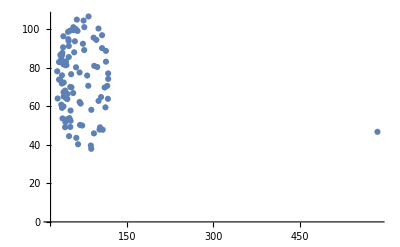
remove one cell that is far away from others:
-Graphics-

```mathematica
dataEmbryo=Import[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures\\102518G6NG_AK9_Features.mx"}]];
```

```mathematica
nucleiFeatures="NucleiFeatures"/.dataEmbryo;
```

```mathematica
Position[nucleiFeatures,{585.5780000000001,46.813,51.}]
```

{{64,8,2}}

```mathematica
nucleiFeaturesNew=Delete[nucleiFeatures,64];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures\\102518G6NG_AK9_Features.mx"}],{"NucleiFeatures"->nucleiFeaturesNew}]
```

#### emb-xim: no littermates

```mathematica
embXimRaw=Import[fNames[[4]]];
```

```mathematica
embXim=MapThread[Rule,{embXimRaw[[1]],#}]&/@embXimRaw[[2;;-1]];
```

```mathematica
embXimPerEmbryo=SplitBy[SortBy[Select[embXim,("Treatment"/.#)=="Littermate"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
embXimPerEmbryo//Length
```

0

#### esc-xim

```mathematica
escXimRaw=Import[fNames[[5]]];
```

```mathematica
escXim=MapThread[Rule,{escXimRaw[[1]],#}]&/@escXimRaw[[2;;-1]];
```

```mathematica
escXimPerEmbryo=SplitBy[SortBy[Select[escXim,("Treatment"/.#)=="Littermate"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
escXimPerEmbryo//Length
```

23

```mathematica
Length/@escXimPerEmbryo
```

{62,30,66,71,81,75,88,116,113,58,64,69,64,74,67,61,59,48,57,59,61,49,65}

```mathematica
escXimPerEmbryo[[1,1]]
```

{id.cluster→0,Experiment→041218Xim_WT_BH.Littermate,Treatment→Littermate,Genotype1→wt,Genotype2→wt,Embryo_ID→041218Xim_WT_BH1,Cell_ID→1,Identity→TE,Size→9969,X→193.49,Y→292.71,Z→4.8075,CH1.Avg→2745.5,CH1.Sum→27400000,CH2.Avg→129.96,CH2.Sum→1300000,CH3.Avg→403.25,CH3.Sum→4020000,CH4.Avg→571.47,CH4.Sum→5700000,CH5.Avg→65.814,CH5.Sum→656000,Cell_cycle→I,Litter→BH,Exp_date→20180412,Img_date→20180503,Gene1→Fgf4,Gene2→any,H_cells→tbd,D_cells→0,Culture_time→0h,Stage.t0→blastocyst,ESC_t0→zero,Cre→none,Technique→NA,Experimenter→NS,MINS_correct→NS,Background→CD1/mixed,ESC_genotype→no.esc,ESC_line→H2B-tdTomato,ES_culture→S/LIF,TE_ICM→TE,Cellcount→62,icm.count→23,group.median→62,Stage→32_64,Channel→CH2,Marker→NANOG.rat,ab.2→af488.rat,CH2.marker→NANOG.rat,CH1.ebLogCor→8.02857,CH2.ebLogCor→4.96176,CH3.ebLogCor→6.11185,CH5.ebLogCor→4.24737,CH3.ebLogCor.x→4.51477,CH5.ebLogCor.x→6.68115,CH1.ebLogCor.s→0.872131,CH2.ebLogCor.s→0.687978,CH3.ebLogCor.s→0.850722,CH5.ebLogCor.s→0.598468,CH3.ebLogCor.xs→0.663098,CH5.ebLogCor.xs→0.882267,Identity.km→TE,CH1.ebLogCor.l→0.872374,CH2.ebLogCor.l→0.687978,CH3.ebLogCor.l→0.850722,CH3.ebLogCor.xl→0.663098,CH5.ebLogCor.xl→0.882267,Identity.hc→TE}

```mathematica
escXimIFRaw=Import[FileNameJoin[{NotebookDirectory[],"References","esc-xim_if.csv"}]];
```

```mathematica
escXimIF=MapThread[Rule,{escXimIFRaw[[1]],#}]&/@escXimIFRaw[[2;;-1]];
```

```mathematica
convertFromSaiz2020[#,escXimIF,"escXim"]&/@escXimPerEmbryo
```

#### ncoms - part of data from 2016

```mathematica
ncomsRaw=Import[fNames[[7]]];
```

```mathematica
ncoms=MapThread[Rule,{ncomsRaw[[1]],#}]&/@ncomsRaw[[2;;-1]];
```

```mathematica
ncomsPerEmbryo=SplitBy[SortBy[Select[ncoms,("Treatment"/.#)=="Littermate"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
ncomsPerEmbryo//Length
```

139

```mathematica
DeleteDuplicates["Experiment"/.ncoms]
```

{020614_R3,020614_R4,032514_R3,032514_R4,041014_R5,041114_R5,050115_R3,050214_R5,050815_R4a,050815_R4b,051514_R3,052714_R4a,052714_R4b,052714_R5a,052714_R5b,052715_R4a,052715_R4b,060414_1,060414_2,060514_1,060915_R3,060915_R4,061014_1,061014_2,061014_3,061014_4,061014_5,071114_1,071914_R3L,072814_R3F,072814_R3P,081715_R6,081815_R6a,081815_R6b,081815_R6c,102214_R4,112415_LM,112415_LMb}

```mathematica
Length/@ncomsPerEmbryo
```

{70,64,74,93,98,109,89,72,76,80,85,50,63,64,37,38,63,50,42,61,63,98,95,93,90,67,87,78,75,76,107,79,70,64,61,55,51,56,86,64,105,79,37,36,49,37,44,62,45,40,37,34,32,43,68,64,58,64,59,70,63,67,64,66,70,76,90,89,114,33,46,63,112,93,102,66,111,38,65,47,64,51,40,32,58,64,44,114,103,124,112,109,108,114,116,92,99,112,88,90,78,100,94,94,61,68,69,64,56,47,81,60,64,33,32,61,134,111,148,127,132,96,100,176,205,178,216,160,125,147,149,120,128,133,166,136,135,200,131}

#### new - no infos on anti-bodies, hence not clear which log correction was used

```mathematica
newRaw=Import[fNames[[8]]];
```

```mathematica
new=MapThread[Rule,{newRaw[[1]],#}]&/@newRaw[[2;;-1]];
```

```mathematica
newPerEmbryoRaw=SplitBy[SortBy[Select[new,("Treatment"/.#)=="Littermate"&&("Genotype1"/.#)=="wt"&],("Embryo_ID"/.#)&],("Embryo_ID"/.#)&];
```

```mathematica
newExperiments=Complement["Experiment"/.newPerEmbryoRaw[[All,1]],"Experiment"/.ablatLMSPerEmbryo[[All,1]],"Experiment"/.compoundsPerEmbryo[[All,1]],"Experiment"/.escXimPerEmbryo[[All,1]]]
```

{030918FVB_A.wt,030918FVB_B.wt,030918FVB_C.wt,031518FVB_D.wt,031618FVB_E.wt,040318FVB_F.wt,040318FVB_G.wt,040518FVB_H.wt,040818FVB_I.wt,042017Pdgfra_AB.wt,042017Pdgfra_AC.wt,042018FVB_J.wt,042018FVB_K.wt,042018FVB_L.wt,042117Pdgfra_AD.wt,051717Pdgfra_AE.wt,052617Pdgfra_AF.wt,052617Pdgfra_AG.wt,052817Pdgfra_AH.wt,061817Pdgfra_AM.wt,062917Pdgfra_AT.wt,071317Pdgfra_AW.wt,073117Pdgfra_BJ.wt,080417Pdgfra_BK.wt,081617_new-lms_A.wt,081617_new-lms_B.wt,081617_new-lms_C.wt,091217Pdgfra_BL.wt,091217Pdgfra_BM.wt,091415_FGF4ko_H.wt,092017Pdgfra_BN.wt,092017Pdgfra_BO.wt,092117Pdgfra_BQ.wt,092217Pdgfra_BR.wt}

```mathematica
newExperiments//Length
```

34

no if info for 091415_FGF4ko _H.wt

```mathematica
newPerEmbryo=Select[newPerEmbryoRaw,MemberQ[newExperiments,"Experiment"/.#[[1]]]&&("Experiment"/.#[[1]])!="091415_FGF4ko_H.wt"&];
```

```mathematica
newPerEmbryo//Length
```

146

```mathematica
newPerEmbryo[[1,1]]
```

{Experiment→030918FVB_A.wt,Genotype1→wt,Litter→A,Embryo_ID→030918FVB_A1,Cell_ID→1,TE_ICM→TE,Cell_cycle→I,Size→7638,X→183.89,Y→270.49,Z→4.1367,CH1.Avg→3534.5,CH1.Sum→2.7×10^7,CH2.Avg→950.8,CH2.Sum→7260000,CH3.Avg→148.35,CH3.Sum→1130000,CH4.Avg→547.16,CH4.Sum→4180000,CH5.Avg→638.12,CH5.Sum→4870000,Exp_date→20180309,Img_date→20180319,Gene1→any,Gene2→any,Genotype2→wt,Background→FVB,Treatment→Littermate,Experimenter→NS,MINS_correct→NS,Cellcount→64,icm.count→30,litter.median→57,Channel→CH2,Marker→CDX2.m,ab.2→af488.m,CH2.marker→CDX2.m,CH1.ebLogCor→8.29894,CH2.ebLogCor→6.98359,CH3.ebLogCor→5.09765,CH5.ebLogCor→6.58944,Stage→64_90,CH3.ebLogCor.x→5.09765,CH5.ebLogCor.x→6.58944,CH1.ebLogCor.s→0.868108,CH2.ebLogCor.s→0.797337,CH3.ebLogCor.s→0.575991,CH5.ebLogCor.s→0.778181,CH3.ebLogCor.xs→0.575991,CH5.ebLogCor.xs→0.778181,Identity.km→TE,CH3.ebLogCor.xl→0.682577,CH5.ebLogCor.xl→0.839886,id.cluster→0,Identity.hc→TE,Identity→TE}

```mathematica
Length/@newPerEmbryo
```

{64,57,63,52,51,58,43,76,63,57,64,58,61,69,93,63,98,60,57,59,167,176,139,146,187,146,129,135,141,113,138,35,40,61,43,64,65,60,64,63,63,59,60,64,59,58,45,63,56,66,63,56,78,74,63,36,32,54,39,62,162,151,203,167,191,172,155,146,115,169,156,156,162,143,183,78,79,63,86,100,147,164,144,137,116,113,80,64,65,60,64,63,54,146,94,117,71,34,76,70,64,64,62,64,63,95,107,106,88,94,83,89,105,90,85,94,109,115,107,97,113,95,101,101,83,65,62,64,82,84,89,107,80,63,96,109,100,83,106,106,88,68,34,51,36,63}

```mathematica
newIFRaw=Import[FileNameJoin[{NotebookDirectory[],"References","new-littermates_if.csv"}]];
```

```mathematica
newIF=MapThread[Rule,{newIFRaw[[1]],#}]&/@newIFRaw[[2;;-1]];
```

```mathematica
newIF[[1]]
```

{Experiment→081617_new-lms_A,Litter→A,Genotype1→wt,Channel→CH1,Marker→DNA,ab.2→Hoechst}

```mathematica
convertFromSaiz2020[#,newIF,"new"]&/@newPerEmbryo
```

## PostProcessing

for some data sets, cns`Private`delaunayCellGraph does not generate a graph object

therefore:
1. Run postprocessing with all files
2. Detect those that do not work
3. Move those from the folder EmbryoFeatures to NoDCG

```mathematica
res=Reap[postProcessingPipelinePositions[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}],"*Features.mx","OutlierDistanceThreshold"->10^6,"EdgeDistanceThreshold"->30,"IncludeSubfolders"->False]];
```

```mathematica
failedFilesRaw=Select[Transpose[{FileBaseName/@FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]],res[[2,1]]}],StringQ[#[[2]]]&]
```

{{042117G6G4_B1_Features,alpha shape failed},{042117G6G4_B4_Features,alpha shape failed},{042117G6G4_B6_Features,alpha shape failed},{042117G6G4_C1_Features,alpha shape failed},{042117G6G4_C2_Features,alpha shape failed},{042117G6G4_C3_Features,alpha shape failed},{042117G6G4_C6_Features,alpha shape failed},{050217G6G4_D5_Features,alpha shape failed},{050217G6G4_D8_Features,alpha shape failed},{052317G6G4_E1_Features,alpha shape failed},{052317G6G4_E3_Features,alpha shape failed},{052317G6G4_E4_Features,alpha shape failed},{052317G6G4_E5_Features,alpha shape failed},{052317G6G4_E7_Features,alpha shape failed},{052317G6G4_E8_Features,alpha shape failed},{052317G6G4_E9_Features,alpha shape failed},{052517G6G4_F10_Features,alpha shape failed},{052517G6G4_F2_Features,alpha shape failed},{052517G6G4_F3_Features,alpha shape failed},{052517G6G4_F4_Features,alpha shape failed},{052517G6G4_F7_Features,alpha shape failed},{052617Pdgfra_AG5_Features,alpha shape failed},{052817Pdgfra_AH3_Features,alpha shape failed},{073117Pdgfra_BJ3_Features,alpha shape failed},{081617_new-lms_C6_Features,alpha shape failed},{102518G6NG_AK3_Features,alpha shape failed}}

```mathematica
failedFiles=Flatten[Table[Select[FileNames["*",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]],StringContainsQ[#,StringTrim[i,"_Features"]]&],{i,failedFilesRaw[[All,1]]}]];
```

```mathematica
RenameFile[#,StringReplace[#,"EmbryoFeatures"->"NoDCG"],OverwriteTarget->True]&/@failedFiles;
```

## Move files for embryos with NANOG.rat

```mathematica
finalFNames=FileNames["*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
(nucleiFeatures="NucleiFeatures"/.Import[#];
If [Flatten[StringCases[Keys[nucleiFeatures[[1]]],"NANOG.rat-"~~___]]!={},
allFiles=FileNames[StringDelete[FileBaseName[#],"_Final"]<>"*.*",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];RenameFile[#,StringReplace[#,"EmbryoFeatures"->"FeaturesRatAb"]]&/@allFiles
])&/@finalFNames
```

## Move files for embryos with GATA6.rb

```mathematica
finalFNames=FileNames["*Final.mx",FileNameJoin[{NotebookDirectory[],"FeaturesRatAb"}]];
```

```mathematica
(nucleiFeatures="NucleiFeatures"/.Import[#];
If [Flatten[StringCases[Keys[nucleiFeatures[[1]]],"GATA6.rb-"~~___]]!={},
allFiles=FileNames[StringDelete[FileBaseName[#],"_Final"]<>"*.*",FileNameJoin[{NotebookDirectory[],"FeaturesRatAb"}]];RenameFile[#,StringReplace[#,"FeaturesRatAb"->"FeaturesG6RbAb"]]&/@allFiles
])&/@finalFNames
```

## Unify notations

staging: Batch, embryo ID, stage by cell number

```mathematica
fileNamesRaw=FileNames["*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
RenameFile[#,StringReplace[#,".mx"->"SaizNotation.mx"]]&/@fileNamesRaw;
```

```mathematica
fNamesSaiz=FileNames["*FinalSaizNotation.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@fNamesSaiz;
```

```mathematica
nucleiFeaturesSaiz=("NucleiFeatures"/.data);
```

```mathematica
(*Select[#,StringMatchQ[Keys[#],"Genotype"~~___]&]&/@nucleiFeaturesSaiz[[All,1]]*)
```

```mathematica
Tally[Flatten["Identity.km"/.nucleiFeaturesSaiz]]
```

{{TE,18045},{DP,2292},{PRE,3735},{EPI,2069},{DN,1025},{NA,545}}

```mathematica
Tally[Flatten["Identity.hc"/.nucleiFeaturesSaiz]]
```

{{TE,18045},{DP,2432},{PRE,3958},{EPI,2494},{EPI.lo,769},{DN,13}}

```mathematica
Grid[Join[{{"Identity.hc","Identity.km","Number of cells"}},ReverseSortBy[Flatten[#,1]&/@Tally[Flatten[{"Identity.hc","Identity.km"}/.nucleiFeaturesSaiz,1]],#[[3]]&]],Spacings->{2,2},Frame->All]
```

Identity.hc | Identity.km | Number of cells
TE | TE | 18045
PRE | PRE | 3648
DP | DP | 2053
EPI | EPI | 1724
EPI.lo | DN | 509
EPI | DN | 412
EPI | NA | 312
DP | EPI | 303
EPI.lo | NA | 207
PRE | DP | 177
PRE | DN | 90
DP | PRE | 72
EPI | DP | 41
PRE | NA | 23
EPI.lo | EPI | 22
EPI.lo | DP | 21
PRE | EPI | 20
EPI.lo | PRE | 10
DN | DN | 10
EPI | PRE | 5
DP | DN | 4
DN | NA | 3

Email from SIlvia on 08/02/2022: “So, use their latest hierarchical clustering…where EPI-low=Epi”

Infos on channel correction

{-Graphics-}

```mathematica
DeleteDuplicates[Flatten[StringCases[Keys[#[[1]]],"NANOG"~~___]]&/@nucleiFeaturesSaiz]
```

{{NANOG.rb-Avg,NANOG.rb-Sum,NANOG.rb-ebLogCor,NANOG.rb-ebLogCor.x,NANOG.rb-ebLogCor.s,NANOG.rb-ebLogCor.xs,NANOG.rb-ebLogCor.xl,NANOG.rb-AvgNorm}}

```mathematica
DeleteDuplicates[Flatten[StringCases[Keys[#[[1]]],"GATA6"~~___]]&/@nucleiFeaturesSaiz]
```

{{GATA6.gt-Avg,GATA6.gt-Sum,GATA6.gt-ebLogCor,GATA6.gt-ebLogCor.x,GATA6.gt-ebLogCor.s,GATA6.gt-ebLogCor.xs,GATA6.gt-ebLogCor.xl,GATA6.gt-AvgNorm},{GATA6.gt-Avg,GATA6.gt-Sum,GATA6.gt-ebLogCor,GATA6.gt-ebLogCor.s,GATA6.gt-ebLogCor.xl,GATA6.gt-AvgNorm}}

use only NANOG.rb and GATA6.gt (to match with 2016 data)

```mathematica
appendRules[nucleusFeatures_]:=
Join[nucleusFeatures,{"TE/ICM"->If[("Identity.hc"/.#)≠"TE","ICM","TE"],"Quadrant"->Switch[("Identity.hc"/.#),"TE","TE","DP","N+G6+","DN","N-G6-","EPI.lo","N-G6-","EPI","N+G6-","PRE","N-G6+"],"Nanog-AvgShifted"->Exp["NANOG.rb-ebLogCor"/.#],
"Gata6-AvgShifted"->Exp["GATA6.gt-ebLogCor"/.#]}&@nucleusFeatures]
```

```mathematica
Table[dataSaiz=Import[#]&@fName;
	nucleiFeatSaiz=("NucleiFeatures"/.dataSaiz);
globalFeatures=("GlobalFeatures"/.dataSaiz);
nucleiFeatures=appendRules/@nucleiFeatSaiz;
genotypeKeys=Flatten[StringCases[Keys[nucleiFeatSaiz[[1]]],"Genotype"~~___]];
staging={"Experiment"/.nucleiFeatures[[1]],"Embryo_ID"/.nucleiFeatures[[1]],"CellNumberStage"/.globalFeatures,(genotypeKeys/.nucleiFeatSaiz[[1]])};
fNameExport=StringReplace[fName,"SaizNotation.mx"->"Data.mx"];
exportData={"NucleiFeatures"->nucleiFeatures,"GlobalFeatures"->globalFeatures,"Staging"->staging};Export[fNameExport,exportData]
,{fName,fNamesSaiz}]
```

## Move files for embryos that are not completely wt

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
(staging="Staging"/.Import[#];
If [DeleteDuplicates[staging[[-1]]]!={"wt"},
allFiles=FileNames[StringDelete[FileBaseName[#],"_Features_FinalData"]<>"*.*",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];RenameFile[#,StringReplace[#,"EmbryoFeatures"->"EmbryoFeaturesNotWT"]]&/@allFiles
])&/@finalFNames
```

## Plot preprocessed data

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
Tally[staging[[All,-2]]]
```

{{3.5,83},{4.,49},{4.5,57},{3.,3}}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{83,49,57}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{1850,1140,2832}

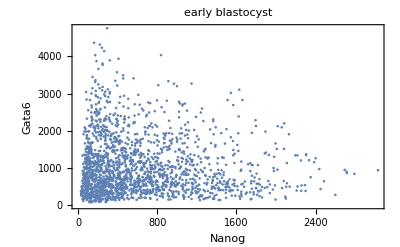
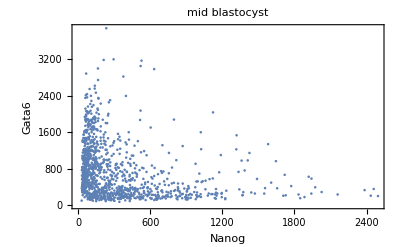
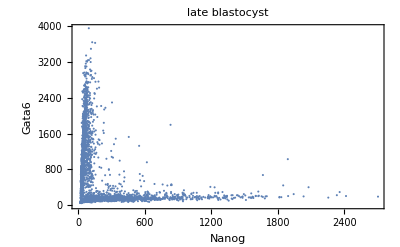
{-Graphics-,-Graphics-,-Graphics-}ICM cells

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

## Genotype statistics

#### no DCG

```mathematica
fNamesNoDCG=FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"NoDCG"}]];
```

```mathematica
dataNoDCG=Import/@fNamesNoDCG;
```

```mathematica
nucleiFeaturesNoDCG="NucleiFeatures"/.dataNoDCG;
```

```mathematica
TableForm[Flatten/@Tally[Table[Sort[Select[nucleiFeaturesNoDCG[[i,1]],StringMatchQ[#[[1]],"Gen"~~___]&]],{i,1,Length[nucleiFeaturesNoDCG]}]]]
```

Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→wt | 4
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→mosaic | 1
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→het | 9
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→wt | 2
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→het | 2
Gene1→Gata6 | Gene2→Gata4 | Genotype1→mosaic | Genotype2→wt | 2
Gene1→Gata6 | Gene2→Gata4 | Genotype1→mosaic | Genotype2→het | 1
Gene1→Pdgfra | Gene2→any | Genotype1→wt | Genotype2→wt | 3
Gene1→any | Gene2→any | Genotype1→wt | Genotype2→wt | 1
Gene1→Gata6 | Gene2→Nanog | Genotype1→wt | Genotype2→het | 1

lost 6 wt

#### NANOG Rat AB, GATA6 Gt

```mathematica
fNamesNRat=FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"FeaturesRatAb"}]];
```

```mathematica
dataNRat=Import/@fNamesNRat;
```

```mathematica
nucleiFeaturesNRat="NucleiFeatures"/.dataNRat;
```

```mathematica
TableForm[Flatten/@Tally[Table[Sort[Select[nucleiFeaturesNRat[[i,1]],StringMatchQ[#[[1]],"Gen"~~___]&]],{i,1,Length[nucleiFeaturesNRat]}]]]
```

Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→ko | 4 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→het | 4 |  | 
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→wt | Genotype3→wt | 27
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→ko | 2 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→mosaic | Genotype2→het | 1 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→het | 4 |  | 
Gene1→Fgf4 | Gene2→any | Genotype1→wt | Genotype2→wt | 9 |  | 
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→mKate/+ | Genotype3→wt | 9
Gene1→Fgf4 | Gene2→any | Genotype1→ko | Genotype2→wt | 4 |  | 
Gene1→Fgf4 | Gene2→any | Genotype1→fl/ko | Genotype2→wt | 3 |  | 
Gene1→any | Gene2→any | Genotype1→wt | Genotype2→wt | 21 |  | 
Gene1→Pdgfra | Gene2→any | Genotype1→wt | Genotype2→wt | 19 |  | 
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→mKate/mKate | Genotype3→wt | 9
Gene1→Fgf4 | Gene2→Pdgfra | Genotype1→ko | Genotype2→het | 1 |  | 
Gene1→Fgf4 | Gene2→Pdgfra | Genotype1→mosaic | Genotype2→wt | 1 |  | 
Gene1→Fgf4 | Gene2→Pdgfra | Genotype1→unknown | Genotype2→wt | 1 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→wt | 1 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→wt | 2 |  |

```mathematica
27+9+21+19+1
```

77

lost 77 wt

#### NANOG Rat AB, GATA6 Rb

```mathematica
fNamesG6Rb=FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"FeaturesG6RbAb"}]];
```

```mathematica
dataG6Rb=Import/@fNamesG6Rb;
```

```mathematica
nucleiFeaturesG6Rb="NucleiFeatures"/.dataG6Rb;
```

```mathematica
TableForm[Flatten/@Tally[Table[Sort[Select[nucleiFeaturesG6Rb[[i,1]],StringMatchQ[#[[1]],"Gen"~~___]&]],{i,1,Length[nucleiFeaturesG6Rb]}]]]
```

Gene1→Pdgfra | Gene2→any | Genotype1→wt | Genotype2→wt | 9

```mathematica
15+4+9
```

28

lost 28 wt

#### EmbryoFeaturesNotWT

```mathematica
fNamesNoWT=FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeaturesNotWT"}]];
```

```mathematica
dataNoWT=Import/@fNamesNoWT;
```

```mathematica
nucleiFeaturesNoWT="NucleiFeatures"/.dataNoWT;
```

```mathematica
Length[nucleiFeaturesNoWT]
```

113

```mathematica
TableForm[Flatten/@Tally[Table[Sort[Select[nucleiFeaturesNoWT[[i,1]],StringMatchQ[#[[1]],"Gen"~~___]&]],{i,1,Length[nucleiFeaturesNoWT]}]]]
```

Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→mosaic | 4 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→wt | 10 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→het | 13 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→het | 3 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→het | Genotype2→mosaic | 1 |  | 
Gene1→Gata6 | Gene2→Nanog | Genotype1→wt | Genotype2→het | 19 |  | 
Gene1→Gata6 | Gene2→Nanog | Genotype1→het | Genotype2→het | 14 |  | 
Gene1→Gata6 | Gene2→Nanog | Genotype1→het | Genotype2→wt | 13 |  | 
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→het | Genotype2→mKate/+ | Genotype3→wt | 4
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→mKate/+ | Genotype3→wt | 26
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→mKate/mKate | Genotype3→wt | 6

#### EmbryoFeatures

```mathematica
fNames=FileNames["*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import/@fNames;
```

```mathematica
nucleiFeatures="NucleiFeatures"/.data;
```

```mathematica
TableForm[Flatten/@Tally[Table[Sort[Select[nucleiFeatures[[i,1]],StringMatchQ[#[[1]],"Gen"~~___]&]],{i,1,Length[nucleiFeatures]}]]]
```

Gene1→any | Gene2→any | Genotype1→wt | Genotype2→wt | 69 |  | 
Gene1→Pdgfra | Gene2→R26 | Gene3→Fgf4 | Genotype1→wt | Genotype2→wt | Genotype3→wt | 80
Gene1→Pdgfra | Gene2→any | Genotype1→wt | Genotype2→wt | 24 |  | 
Gene1→Gata6 | Gene2→Gata4 | Genotype1→wt | Genotype2→wt | 6 |  | 
Gene1→Gata6 | Gene2→Nanog | Genotype1→wt | Genotype2→wt | 13 |  |

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,44},{N+G6+,1070},{N+G6-,293},{N-G6+,443}},{{N-G6-,31},{N+G6+,344},{N+G6-,274},{N-G6+,491}},{{N-G6-,324},{N+G6+,50},{N+G6-,888},{N-G6+,1570}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,44},{N+G6+,1070},{N+G6-,293},{N-G6+,443}},{{N-G6-,31},{N+G6+,344},{N+G6-,274},{N-G6+,491}},{{N-G6-,324},{N+G6+,50},{N+G6-,888},{N-G6+,1570}}}

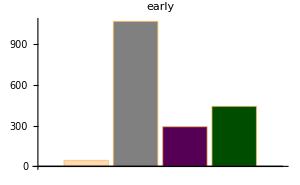
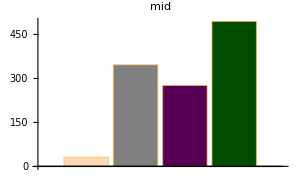
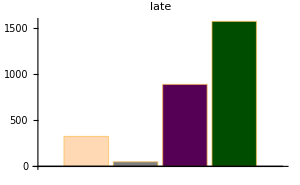

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

## ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{26,13,30,10,15,18,14,26,21,21,9,9,19,22,15,21,5,17,13,23,22,18,7,6,13,17,15,9,15,21,26,17,24,24,20,30,22,11,14,10,6,8,11,14,10,28,16,13,18,14,16,12,5,15,16,19,19,16,18,18,17,14,10,9,14,20,4,24,7,17,19,20,10,14,15,17,20,25,13,23,27,23,21},{11,13,12,18,18,10,16,14,14,11,9,15,6,7,10,16,0,1,8,14,12,16,9,18,9,15,16,9,13,12,12,16,12,13,8,10,7,11,17,16,17,25,11,17,9,20,15,13,17},{19,18,27,14,32,20,4,23,16,11,17,10,17,7,8,40,24,10,37,29,28,18,27,33,24,20,7,13,1,10,6,4,12,11,10,10,14,18,16,15,13,17,14,9,17,6,15,13,20,20,18,12,27,12,11,16,18}}

```mathematica
Length/@nanogPositiveByStage
```

{83,49,57}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{4,7,0,12,5,8,3,3,4,6,7,14,9,2,3,2,13,11,5,5,9,0,10,8,2,0,10,9,9,5,2,7,0,3,4,2,3,12,0,3,10,11,13,6,10,3,0,0,1,1,14,13,14,6,3,4,3,2,12,1,6,0,0,25,7,2,23,1,9,10,6,0,15,1,1,3,6,5,7,6,0,5,1},{12,14,5,9,9,11,14,10,9,9,10,14,16,17,9,13,17,26,15,9,12,9,12,18,18,7,3,14,10,7,11,7,14,8,10,9,10,13,8,9,6,3,12,8,13,3,11,7,2},{12,18,40,69,23,30,67,32,31,18,26,9,28,43,39,45,40,68,30,30,26,16,42,35,40,40,26,34,72,35,58,47,34,22,31,16,20,15,14,19,13,37,84,82,26,31,20,23,23,25,40,24,9,23,40,19,35}}

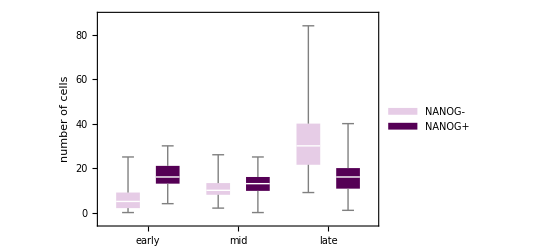

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{29,11,15,14,17,13,13,27,17,23,10,17,21,17,13,21,14,24,16,24,28,16,16,13,11,16,20,12,19,24,23,12,19,18,13,21,19,19,14,13,7,10,16,11,9,30,14,13,15,14,20,14,13,18,19,23,22,17,30,19,20,14,10,26,21,21,25,19,14,21,25,20,20,14,15,16,25,28,18,29,27,27,22},{12,15,9,26,25,17,29,15,23,10,16,20,12,15,8,16,10,20,15,18,20,18,15,17,21,20,12,16,19,13,15,20,15,11,11,17,14,15,22,18,19,28,21,23,16,23,16,14,15},{15,19,38,38,25,30,31,28,31,18,26,10,24,37,26,45,40,40,25,24,26,16,35,32,38,29,27,31,53,35,42,40,28,17,24,17,21,24,14,22,13,31,56,55,23,25,20,24,25,31,39,16,20,24,32,17,28}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{1,9,15,8,3,13,4,2,8,4,6,6,7,7,5,2,4,4,2,4,3,2,1,1,4,1,5,6,5,2,5,12,5,9,11,11,6,4,0,0,9,9,8,9,11,1,2,0,4,1,10,11,6,3,0,0,0,1,0,0,3,0,0,8,0,1,2,6,2,6,0,0,5,1,1,4,1,2,2,0,0,1,0},{11,12,8,1,2,4,1,9,0,10,3,9,10,9,11,13,7,7,8,5,4,7,6,19,6,2,7,7,4,6,8,3,11,10,7,2,3,9,3,7,4,0,2,2,6,0,10,6,4},{16,17,29,45,30,20,40,27,16,11,17,9,21,13,21,40,24,38,42,35,28,18,34,36,26,31,6,16,20,10,22,11,18,16,17,9,13,9,16,12,13,23,42,36,20,12,15,12,18,14,19,20,16,11,19,18,25}}

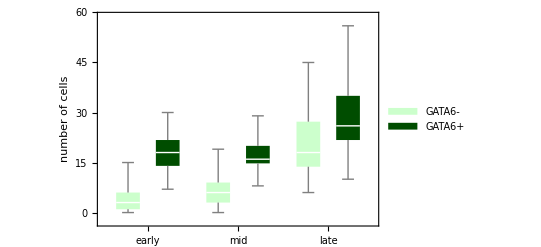

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{83,49,57}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```